```mathematica
data=Import["C:\\Users\\Я\\Desktop\\machine-learning-ex6\\ex6\\ex6data2.mat","Data"];
```

```mathematica
data[[2]]=Flatten[data[[2]]];
```

```mathematica
data=SortBy[data,Last];
```

```mathematica
Y=data[[2]][[;;]]/.{0.->{1.,0.},1.->{0.,1.}};
X=data[[1]][[;;]];
X1=Table[If[data[[2]][[i]]==0.,data[[1]][[i]],Nothing],{i,1,Length[data]}];
X2=Table[If[data[[2]][[i]]==1.,data[[1]][[i]],Nothing],{i,1,Length[data]}];
```

Part::partw: Part 4 of {-0.092742,0.68494,1} does not exist.

Part::partw: Part 5 of {-0.092742,0.68494,1} does not exist.

Part::partw: Part 6 of {-0.092742,0.68494,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of {-0.092742,0.68494,1} does not exist.

Part::partw: Part 5 of {-0.092742,0.68494,1} does not exist.

Part::partw: Part 6 of {-0.092742,0.68494,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

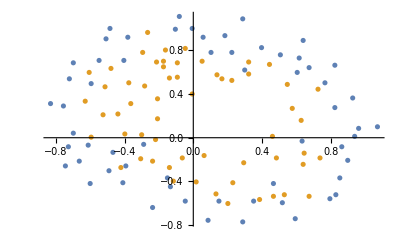

```mathematica
ListPlot[{X1,X2}]
```

```mathematica
X=Flatten[{X1,X2},1];
Y=Table[If[i≤ Length[X1],{1.,0.},{0.,1.}],{i,1,Length[X]}]
```

{{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.},{0.,1.}}

```mathematica
Q[w_]:=1/Length[X] Sum[(Y[[i]]-h[X[[i]],w])ᵀ(Y[[i]]-h[X[[i]],w]),{i,1,Length[X]}]
```

```mathematica
Q1[w_]:=1/Length[X] Sum[Boole[Round[h[X[[i]]],w]-Y[[i]]],{i,1,Length[X]}]
```

```mathematica
Q[w_]:=Sum[Log[1+Exp[-Y[[i]].h[X[[i]],w]]],{i,1,Length[X]}]
```

```mathematica
data[[2]][[500]]
```

1.

```mathematica
Q1[ww1]
```

$Aborted[]

Context::notfound: Symbol Removed[$$Failure] not found.

General::stop: Further output of Context::notfound will be suppressed during this calculation.

$Aborted[]

Thread::tdlen: Objects of unequal length in {{{{0.00264006 Removed[$$Failure],0.00687235 Round[Times[«2»]]},{0.00283882 Round[Times[«2»]],0.00383581 Removed[$$Failure]},{0.00138825 Removed[$$Failure],0.00390231 Removed[$$Failure]},«5»,{0.00488023 Removed[$$Failure],0.00498587 Removed[$$Failure]},{0.00436113 Round[Times[«2»]],0.00584019 Removed[$$Failure]}},{{«1»},{«1»}}},«1»,{«1»}}+«1» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

$Aborted[]

```mathematica
ww1=traingraddecent1[X,Y,{2,10,2},1,0,100];
```

```mathematica
h[X[[1]],ww1]
```

{0.471831,0.528496}

```mathematica
x1
```

x1

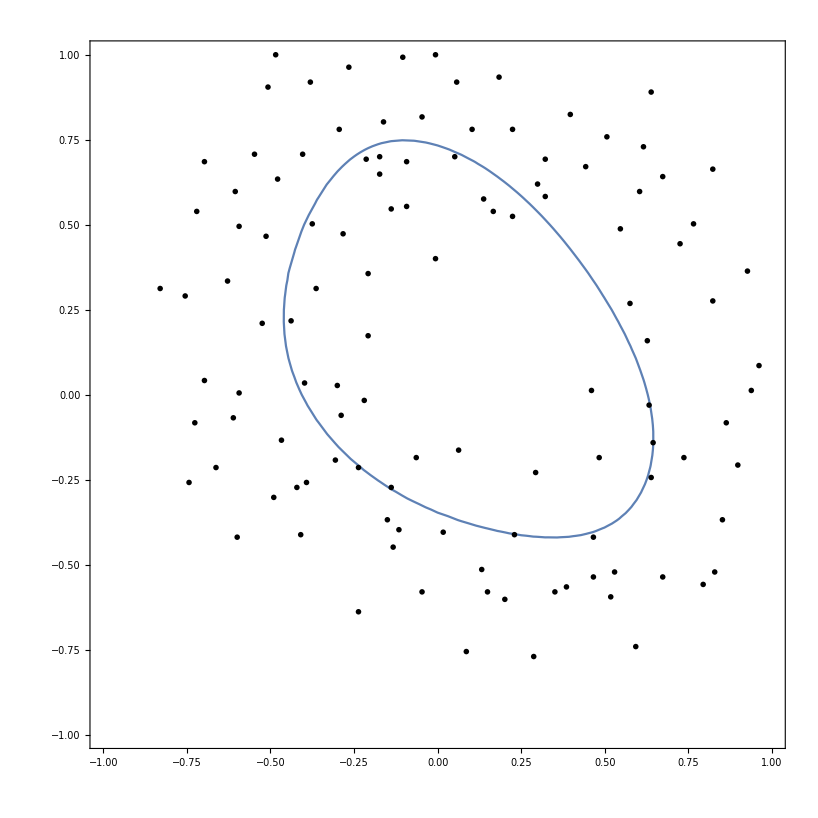

```mathematica
Show[ContourPlot[h[{xx,xxx},ww1][[1]]==0.5,{xx,-1,1},{xxx,-1,1}],ListPlot[{X1,X2},PlotTheme->"Monochrome"]]
```

```mathematica
ww=traingraddecent[X,Y,{2,4,2},5,10^-5,500];
```

```mathematica
ww1=trainSLayer[X,Y,{2,5,2},1,0,1000];
ww1[[1]][[1]]
```

{{-0.302813,-2.58225},{-0.422076,0.0106948},{-0.16978,0.0205513},{-1.88752,0.904794},{-2.78452,-1.7323}}

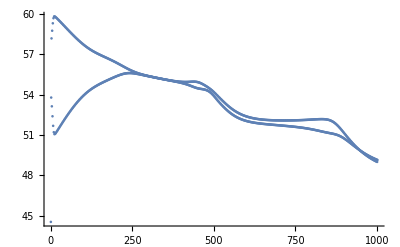

```mathematica
ListPlot[Table[Q[ww1[[3]][[i]]],{i,1,Length[ww1[[3]]]}]]
```

```mathematica
sigma[x_]:=Tanh[x];
dsigma[x_]:=1-Tanh[x]^2
```

```mathematica
sigma[x_]:=(1.+Exp[-x])^-1
dsigma[x_]:=sigma[x](1.-sigma[x])
```

```mathematica
Timing[ww=Module[{steps=400,η=15,λ=0,m=Length[X],er={},s=3,s1=2,s2=4,d2,d3,s3=3,g,i,j,k,w1,w2,iter,z2,z3,y2,y3,y1,b1,b2,db1,db2,dw1,dw2},
w1=RandomReal[{-.1,0.1},{s2,s1}];
w2=RandomReal[{-.1,0.1},{s3,s2}];
b1=Table[1,{i,s2}];
b2=Table[1,{i,s3}];
AppendTo[er,{w1,b1,w2,b2}];
For[iter=1,iter≤steps,iter++,
dw1=Table[0,{i,s2},{j,s1}];
dw2=Table[0,{i,s3},{j,s2}];
db1=Table[0,{i,s2}];
db2=Table[0,{i,s3}];
For[g=1,g≤m,g++,
y1=X[[g]];
z2=b1+w1.y1;
y2=sigma[z2];
z3=w2.y2+b2;
y3=sigma[z3];
d3=-(Y[[g]]-y3)*dsigma[z3];
d2=(w2ᵀ.d3)*dsigma[z2];
Table[dw1[[i,j]]+=d2[[i]]y1[[j]],{i,Length[d2]},{j,Length[y1]}];
Table[dw2[[i,j]]+=d3[[i]] y2[[j]],{i,Length[d3]},{j,Length[y2]}];
db1+=d2;
db2+=d3;
];
w2=w2(1-λ/m)-η/m dw2;
w1=w1(1-λ/m)-η/m dw1;
b1=b1-η/m db1;
b2=b2-η/m db2;
AppendTo[er,{w1,b1,w2,b2}];
];
{w1,b1,w2,b2,er}]]
```

{3.84375,{{{4.68959,5.70969},{0.0851655,0.791164},{2.22927,3.99739},{-1.44635,-2.87343}},3,{{{{0.0847425,0.0180211},{0.00442634,0.0661802},{-0.0432318,0.0940915},{-0.0297349,-0.0612515}},{1,1,1,1},1,{1,1,1}},399,{1}}}}
 |  |  |  |

```mathematica
h[x_,W_]:=Module[{a2,a3},
a2=sigma[Table[Sum[W[[1]][[i,j]]x[[j]],{j,1,Length[x]}]+W[[2]][[i]],{i,1,Length[W[[1]]]}]];
sigma[Table[Sum[W[[3]][[i,j]]a2[[j]],{j,1,Length[a2]}]+W[[4]][[i]],{i,1,Length[W[[3]]]}]]]
```

```mathematica
Q[w_]:=1/2 Sum[Norm[(h[X[[i]],w]-Y[[i]])]^2,{i,1,Length[X]}]
```

```mathematica
Q[ww]
```

0.0803644

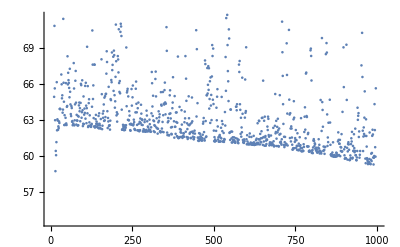

```mathematica
ListPlot[Table[Q[ww[[3]][[i]]],{i,1,Length[ww[[3]]]}]]
```

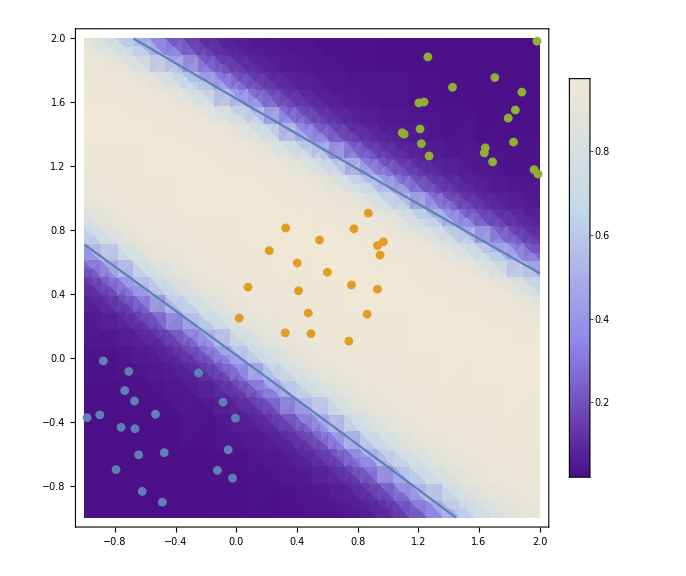

```mathematica
Show[{DensityPlot[h[{x1,x2},ww][[2]],{x1,-1,2},{x2,-1,2},PlotLegends->Automatic,ImageSize->Large,PlotTheme->"Classic"],ListPlot[{X11,X22,X33}],ContourPlot[h[{x1,x2},ww][[2]]==0.5,{x1,-1,2},{x2,-1,2}]}]
```

```mathematica
trainSLayer[X_,Y_,s_,η_,λ_,steps_]:=Module[{m=Length[X],er={},ns=Length[s],d,g,i,j,k,iter,y,b,w,z,a,dw,db},
w=Table[RandomReal[{-.1,0.1},{s[[i+1]],s[[i]]}],{i,1,ns-1}];
b=Table[Table[1,{i,s[[i+1]]}],{i,1,ns-1}];
AppendTo[er,{w,b}];
For[iter=1,iter≤steps,iter++,
dw=Table[Table[0,{j,s[[i+1]]},{k,s[[i]]}],{i,1,ns-1}];
db=Table[Table[0,{j,s[[i+1]]}],{i,1,ns-1}];
For[g=1,g≤m,g++,
a[1]=X[[g]];
Table[z[i]=w[[i-1]].a[i-1]+b[[i-1]];
a[i]=sigma[z[i]];,{i,2,ns}];
d[ns]=-(Y[[g]]-a[ns])*dsigma[z[ns]];
Table[d[k]=w[[k]]ᵀ.d[k+1]*dsigma[z[k]];,{k,ns-1,2,-1}];
Table[dw[[k]]+=Partition[d[k+1],1].Partition[a[k],Length[a[k]]];,{k,1,ns-1}];
Table[db[[k]]+=d[k+1];,{k,1,ns-1}];
];
w=w(1-(λ η)/m)-η/m dw;
b=b-η/m db;
AppendTo[er,{w,b}];
];
{w,b,er}]
```

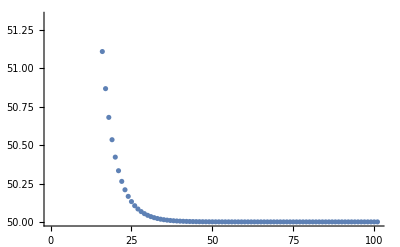

```mathematica
ww=trainSLayer[X,Y,{3,5,5,5,5,5,5,3},0.5,0.,100];
ListPlot[Table[Q[ww[[3]][[i]]],{i,1,Length[ww[[3]]]}]]
```

```mathematica
Q[w_]:=1/2 Sum[Norm[(h[X[[i]],w]-Y[[i]])]^2,{i,1,Length[X]}]
```

```mathematica
h[x_,w_]:=Module[{a,z,ns=Length[w[[1]]]+1},
a[1]=x;
Table[z[i]=w[[1]][[i-1]].a[i-1]+w[[2]][[i-1]];
a[i]=sigma[z[i]];,{i,2,ns}];
a[ns]
]
```

```mathematica
Show[ContourPlot3D[Evaluate[h[{x1,x2,x3},ww][[2]]==0.5],{x1,0,6},{x2,0,6},{x3,0,3},PlotLegends->Automatic,ImageSize->Large,PlotTheme->"Classic",AxesLabel->{x1,x2,x3}],ListPointPlot3D[Partition[X,50],PlotStyle->PointSize[.01],Filling->Axis]]
```

-Graphics3D-

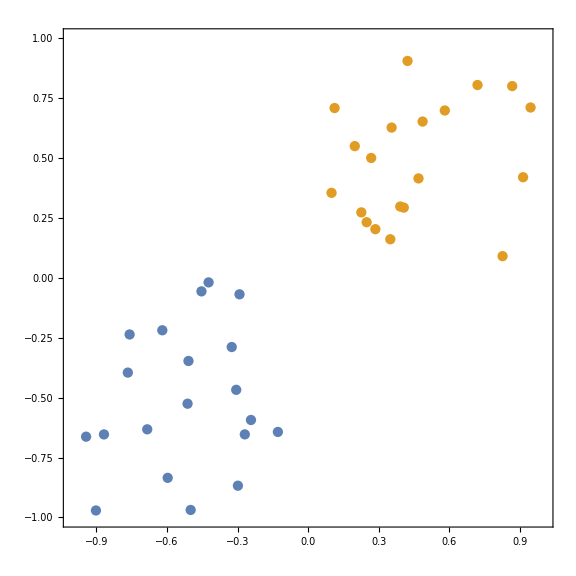

```mathematica
Show[{ContourPlot[Evaluate[h[{x1,x2},ww][[2]]==0.5],{x1,-1,1},{x2,0-1,1},PlotLegends->Automatic,ImageSize->Large,PlotTheme->"Classic"],ListPlot[{X11,X22}]}]
```

```mathematica
ld1=ld[[;;,{2,3,4,5}]];
```

```mathematica
X=ld1[[;;,{1,2,3}]];
Y=ld1[[;;,4]]/.{"Iris-setosa"->{1,0,0},"Iris-versicolor"->{0,1,0},"Iris-virginica"->{0,0,1}};
```

```mathematica
ListPlot3D[Partition[X,50]]
```

-Graphics3D-

```mathematica
ww=trainSLayer[{2,4,3}];
```

```mathematica
data=Import["C:\\Users\\Я\\Desktop\\machine-learning-ex2\\ex2\\ex2data2.txt","Data"];
```

```mathematica
data[[1]][[3]]
```

1

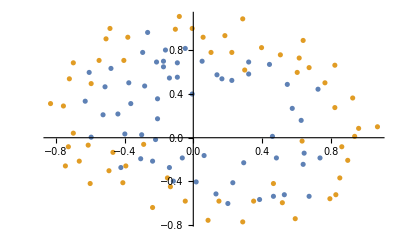

```mathematica
X=data[[;;,{1,2}]];
Y=data[[;;,3]];
X1=Table[If[data[[i]][[3]]==1,data[[i,{1,2}]],Nothing],{i,1,Length[data]}];
X2=Table[If[data[[i]][[3]]==0,data[[i,{1,2}]],Nothing],{i,1,Length[data]}];
ListPlot[{X1,X2}]
```

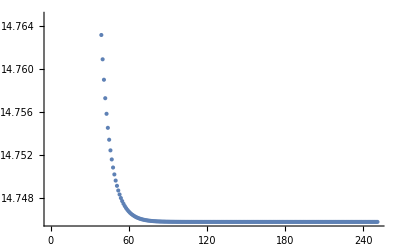

```mathematica
ww=trainSLayer[X,Y,{2,5,5,5,5,5,5,5,5,5,1},10,0.,250];
ListPlot[Table[Q[ww[[3]][[i]]],{i,1,Length[ww[[3]]]}]]
```

```mathematica
Show[ListPlot[{X1,X2}],ContourPlot[h[{x1,x2},ww]==0.5,{x1,-1,1},{x2,-1,1}]]
```

$Aborted